# Vaje za 7. teden

6. 4. in 7. 4. 2022

## Osnovne definicije

Trikotnik definiramo kot seznam treh točk. Vsaka točka je seznam (par dveh števil)
Funkcija Stranice vrne seznam parov točk, ki predstavljajo stranice.
Funkcija Koti vrne seznam trojic točk, ki predstavljajo kote.

```mathematica
ClearAll[Stranice, Koti, SlikaOglisc, SlikaStranic]
(* V tej celici so že pripravljene definicije funkcij, ki bodo prišle prav - ni jih treba spreminjati. *)

(* Za trikotnik podan s seznamom točk definiramo funkciji za stranice in kote *)
Stranice[{AA_,BB_,CC_}] :={{BB, CC},{CC, AA}, {AA, BB}}
Koti[{AA_,BB_,CC_}] := {{CC, AA, BB},{AA, BB, CC},{BB, CC, AA}}

(* Definiramo funkciji, ki nam vrneta seznama grafičnih elementov za točke in stranice *)
SlikaOglisc[trikotnik_] := Point[trikotnik]
SlikaStranic[trikotnik_] := Line[Stranice[trikotnik]] 

(* Risanje trikotnika: določimo še barvo, velikost točke, ter debelino črt *)
NarisiTrikotnik[trikotnik_]:=
Graphics[{
GrayLevel[0.7],PointSize[0.02],Thickness[0.005],
SlikaOglisc[trikotnik], 
SlikaStranic[trikotnik]
}]
```

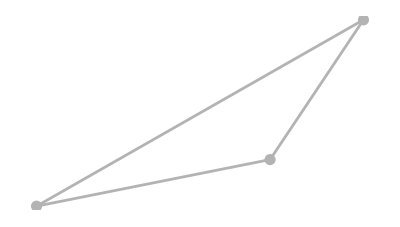

```mathematica
(* Primer uporabe *)
trikotnik={{0,0},{5,1},{7,4}};
NarisiTrikotnik[trikotnik]
```

## Naloga 1

Narišite še en trikotnik

## Simetrale

## Naloga 2

1. Definirajte funkcijo SimetralaKota, ki vrne daljico, ki predstavlja nosilec simetrale kota {a, b, c} z izhodiščem v točki b. Funkcija naj sprejme kot podan s trojico točk in dolžino nosilca, ter vrne koordinati krajišč.
2. Funkcijo definirajte s pomočjo pomožne funkcije VektorSimetraleKota, ki vrne vektor simetrale. Pomagajte si s funkcijo Normalize, ki vrne normaliziran vektor.
3. Naredite grafične objekte za vse tri simetrale kota v trikotniku in jih dodajte v sliko zgoraj. Funkcijo dopolnite tako, da ji dodate opcijski parameter Simetrale, s katerim lahko vklopite ali izklopite risanje simetral (spodaj je enostaven primer). Simetrale narišite bodisi kot vektorje, bodisi kot premice s funkcijo InfiniteLine.

```mathematica
ClearAll[SimetralaKota]
(* 10 je privzeta dolžina vektorja *)
(* Implementaciji seveda nista pravilni, popravite ju. *)
VektorSimetraleKota[{x_,y_,z_}]:=Normalize[Normalize[x-y]+Normalize[z-y]]
SimetralaKota[{x_,y_,z_},dolzina_:10] := {y,y+dolzina+VektorSimetraleKota[{x,y,z}]}


(* Simetrala prvega kota v trikotniku *)
SimetralaKota[First[Koti[trikotnik]]]
```

{{4,7},{14+(1/(√2)-2/(√29))/(√((1/(√2)-2/(√29))^2+(1/(√2)+5/(√29))^2)),17+(-1/(√2)-5/(√29))/(√((1/(√2)-2/(√29))^2+(1/(√2)+5/(√29))^2))}}

Primer risanja z opcijskim parametrom Risi

```mathematica
ClearAll[Slika, Risi]
Slika[tocka_, OptionsPattern[Risi->False]]:=
Graphics[{
PointSize[0.1],
If[OptionValue[Risi],
Point[tocka], (* Kaj naredimo, če je pogoj izpolnjen *)
{} (* Kaj naredimo sicer *)
]
}]
Slika[{0,0}]
Slika[{0,0},Risi->True]
```

Na sliko dorišite še točko, v kateri se sekajo simetrale. Pri reševanju enačbe si pomagajte s funkcijo Solve.
Ta točka je središče včrtane krožnice.

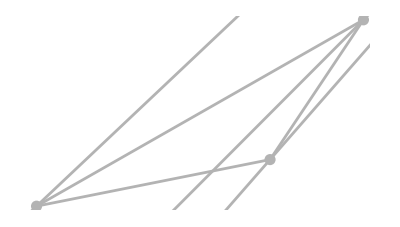

```mathematica
ClearAll[NarisiTrikotnik]
NarisiTrikotnik[trikotnik_, OptionsPattern[RisiSimetrale->False]]:=(* premice bi se mogle sekat ne bit vzporedne, verjetno zgoraj kej manjka*)
Graphics[{
GrayLevel[0.7],PointSize[0.02],Thickness[0.005],
SlikaOglisc[trikotnik], 
SlikaStranic[trikotnik],
If[OptionValue[RisiSimetrale],
Table[
InfiniteLine[SimetralaKota[kot]],
{kot, Koti[trikotnik]}
],
{}
]
}]
NarisiTrikotnik[trikotnik, RisiSimetrale->True]
```

```mathematica
(* Simetrala kota {x,y,z} kot linearna funkcija *)
Simetrala[{x_,y_,z_},t_] :=y+t*VektorSimetraleKota[{x,y,z}]
Sredisce[trikotnik_]:=Simetrala[First[Koti[trikotnik]],r]/.Solve[Simetrala[First[Koti[trikotnik]],r]==Simetrala[Last[Koti[trikotnik]],s],
(r,s)]//First
Sredisce[trikotnik](*tle pride ful dolga rešitev*)

NarisiTrikotnik[trikotnik_, OptionsPattern[RisiSimetrale->False]]:=
Graphics[{
GrayLevel[0.7],PointSize[0.02],Thickness[0.005],
SlikaOglisc[trikotnik], 
SlikaStranic[trikotnik],
If[OptionValue[RisiSimetrale],
Prepend[
Table[
InfiniteLine[SimetralaKota[kot]],
{kot, Koti[trikotnik]}
],
Point[Sredisce[trikotnik]]
],
{}
],
Circle[Sredisce[trikotnik],S]
}]
NarisiTrikotnik[trikotnik, RisiSimetrale->True]
```

## Včrtana krožnica

## Naloga 3

Narišite včrtani krog. Pomagate si lahko s spodnjo funkcijo.

```mathematica
RazdaljaPremicaTocka[{x_, y_}, {a_, b_}, {c_, d_}] := Cross[{x, y, 0} - {a, b, 0}, Normalize[{c, d, 0} - {a, b, 0}]]//Norm
```

```mathematica
Simetrala[{x_,y_,z_},t_] :=y+t*VektorSimetraleKota[{x,y,z}]
Sredisce[trikotnik_]:=Simetrala[First[Koti[trikotnik]],r]/.Solve[Simetrala[First[Koti[trikotnik]],r]==Simetrala[Last[Koti[trikotnik]],s],
(r,s)]//First
Sredisce[trikotnik](*tle pride ful dolga rešitev*)

NarisiTrikotnik[trikotnik_, OptionsPattern[RisiSimetrale->False]]:=
Graphics[{
GrayLevel[0.7],PointSize[0.02],Thickness[0.005],
SlikaOglisc[trikotnik], 
SlikaStranic[trikotnik],
If[OptionValue[RisiSimetrale],
Prepend[
Table[
InfiniteLine[SimetralaKota[kot]],
{kot, Koti[trikotnik]}
],
Point[Sredisce[trikotnik]]
],
{}
],
Circle[
Sredisce[trikotnik],
RazdaljaPremicaTocka[Sredisce[trikotnik],First[Stranice[trikotnik]]]
]
}]
NarisiTrikotnik[trikotnik, RisiSimetrale->True]
```